# Proyecto 1: Péndulo doble

En el artículo

los autores investigan la sección de Poincaré para la dinámica del péndulo doble.

descrito por el sistema de ecuaciones:

Los autores encuentran que para obtener una buena sección de Poincaré conviene tomarlas alrededor de los puntos críticos

usando los siguientes valores de energía como valor de cruce para tomar una sección de Poincaré:

Tomando en cuenta que la energía cinética del sistema está dada por:

y la energía potencial

--Graphics-

El objetivo del proyecto es obtener la sección de Poincaré y calcular a partir de qué condiciones iniciales se da la transición entre trayectorias regulares a trayectorias caóticas.

```mathematica
DPPoincare[θ1Initial_,θ2Initial_,tMax_]:=Block[{m1=3,m2=1,l=1,g=1,θ1,θ2,solution},
(* Solución numérica *)
solution = Quiet@Reap[NDSolveValue[
{
θ1''[t]==(-g*( 2*m1+m2 )*Sin[θ1[t]]-m2*g*Sin[θ1[t]-2*θ2[t]]-2*Sin[θ1[t]-θ2[t]]*m2*( l*(θ2'[t]^2 )+( θ1'[t]^2 )*Cos[θ1[t]-θ2[t]] ))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])), θ2''[t]==(2*Sin[θ1[t]-θ2[t]]*(g*(m1+m2)*Cos[θ1[t]]+l*((θ2'[t]^2)*m2*Cos[θ1[t]-θ2[t]]+(θ1'[t]^2)*(m1+m2))))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])),
θ1[0] == θ1Initial, θ2[0] == θ2Initial, θ2'[0] == 0, θ1'[0] == 0,
WhenEvent[θ1[t]==0 && θ1'[t]>0,Sow[{θ2[t],θ2'[t]}]]
},
{θ1,θ2},{t,0,tMax},
AccuracyGoal->40,MaxSteps->10^6
]][[2]];
If[solution ≠{},First[solution],Nothing]
];
```

## Variando θ_1

Regiones estables

```mathematica
poincare = Table[{θ1,DPPoincare[θ1,0,1000]},{θ1,0.1,1,0.1}];
```

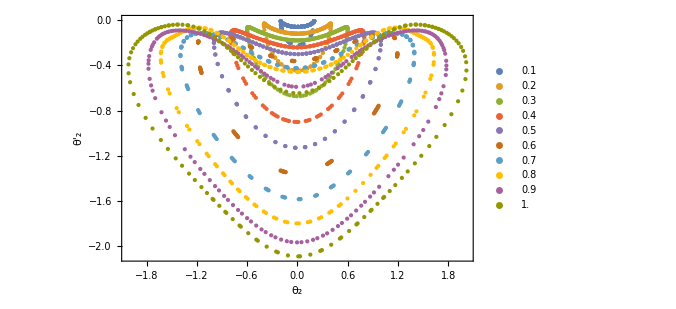

```mathematica
ListPlot[
poincare[[All,2]],
PlotRange->All,
Frame->True,
PlotLegends->poincare[[All,1]],
PlotStyle->PointSize[Medium],
ImageSize->500,
FrameLabel->{"θ_2","θ'_2"}
]
```

Transición al caos

```mathematica
poincare = Table[{θ1,DPPoincare[θ1,0,1000]},{θ1,0.5,1.2,0.1}];
```

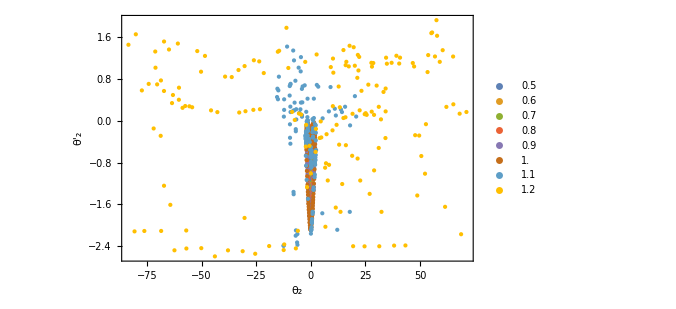

```mathematica
ListPlot[
poincare[[All,2]],
PlotRange->All,
Frame->True,
PlotLegends->poincare[[All,1]],
PlotStyle->PointSize[Medium],
ImageSize->500,
FrameLabel->{"θ_2","θ'_2"}
]
```

Caos suave

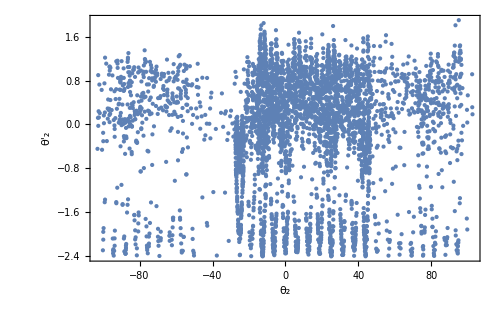

```mathematica
ListPlot[
DPPoincare[1.1,0,180000],
PlotRange->All,
Frame->True,
PlotStyle->PointSize[Medium],
ImageSize->500,
FrameLabel->{"θ_2","θ'_2"}
]
```

Caos duro

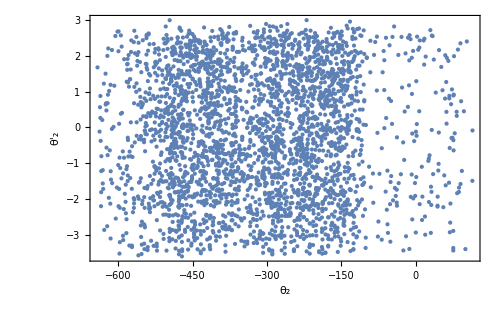

```mathematica
ListPlot[
DPPoincare[1.8,0,180000],
PlotRange->All,
Frame->True,
PlotStyle->PointSize[Medium],
ImageSize->500,
FrameLabel->{"θ_2","θ'_2"}
]
```

## Variando θ_2

```mathematica
poincare = Table[{θ2,DPPoincare[0.5,θ2,1000]},{θ2,0,0.4,0.1}];
```

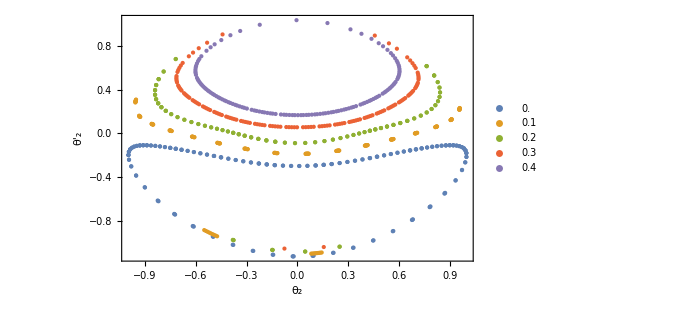

```mathematica
ListPlot[
poincare[[All,2]],
PlotRange->All,
Frame->True,
PlotLegends->poincare[[All,1]],
PlotStyle->PointSize[Medium],
ImageSize->500,
FrameLabel->{"θ_2","θ'_2"}
]
```

## Variando θ_1 y θ_2

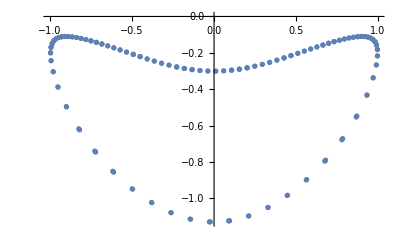

```mathematica
puntos = DPPoincare[0.5,0,1000];
ListPlot[puntos]
```

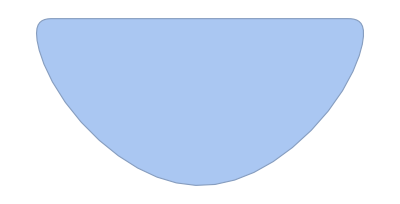

```mathematica
ConvexHullMesh[puntos]
```

```mathematica
Area[ConvexHullMesh[puntos]]
```

1.52026

```mathematica
CalculaArea[pts_]:=If[pts===Nothing || pts=={},Return[0.0],Area[ConvexHullMesh[pts]]];
```

```mathematica
areas = Flatten[ParallelTable[{θ1,θ2,CalculaArea[DPPoincare[θ1,θ2,3000]]},{θ1,-π,π,0.1},{θ2,-π,π,0.1}],1];
```

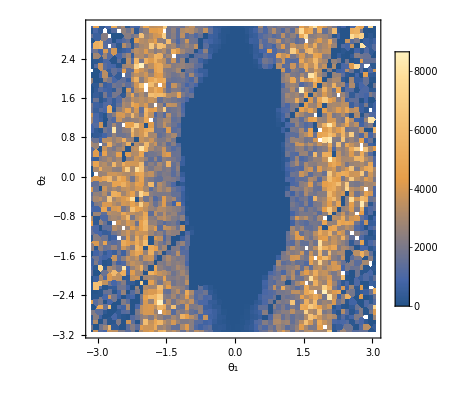

```mathematica
ListDensityPlot[areas,
InterpolationOrder->0,
FrameLabel->{"θ_1","θ_2"},
PlotLegends->Automatic
]
```